# Penrose Encoding and graph visualization.

## Diana Itzel Vázquez Santiago. Emmanuel Isaac Juárez Caballero. Jesús Eduardo Hermosilla Díaz. Maestría en Inteligencia Artificial, generación 2021-2023

## Initializing Cells

```mathematica
(*Starting Executing Cells*)
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
FindExternalEvaluators["Python"]
session=StartExternalSession["Python"]
```

ExternalSessionObject[…]

## Execution of the python code for the penrose Encoding.

```mathematica
NotebookDirectory[]
```

C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\

```mathematica
FileNames["*","C:\\Users\\emman\\OneDrive\\Documentos\\GitHub\\PenroseEncodingFinalProyect\\"]
```

{C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\decoderTM.py,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.git,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.gitattributes,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.idea,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.ipynb_checkpoints,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\LICENSE,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\nuniversal.txt,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\penrose_encoding.py,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\procesado.csv,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\PruebasDecoderTM.ipynb,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\README.md,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\salida.csv,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\Turing.nb,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\universal.txt}

```mathematica
u=Import["nuniversal.txt"]//ToExpression;
n=u;
ExternalEvaluate[session,File["penrose_encoding.py"]];
PenroseEncoding=ExternalEvaluate[session,"codificacion"];
execution=PenroseEncoding[n];
```

TM after Penrose Coding:  R100000001L10R10010111R100R100110000R110R10011101R1000R10011011R1010L10110101L1100L11101011L1110R100110011R10000R101000011R10010L101100011L10100L101110001L10110R10001000L11000L110001010L100111R11011R10000R11101R1010100R10000000R100000L1101111L100010L101111111L1000111L100011001L100110R101000110R1011010R101001R11001L101011L101100L11011010L1111000R101111L1101001R110001R110010R11111001R101110101R110101L111011L110110R111000L100101011L111011L1110000L11010000R111101L11011R10010100L1000000L101101111L101101011L1000011L1000100L100001110L1000110L100001001L1001000L100010110L10010001R1001101L1001101R10100001R100111010R1001111L1010000L10101111L11110R1010011R1010101R10000001R10000100R10000101R100000000R1011001L1011100R1011011R1000010L1011101R1010L110000011L1100000R11100111R10111R1100011L1101011L1100101R11010001L100000L1101001R110110R111001L1101101L11100001L11100001L100000L11100011L10111R1110001L1100111L1110101L1111000L11000000L10101000R10101001R111110L100000001R101000R1111101L101000R10100111L1000100L1001000L1000R10000001R10000101L1110111R100100101L1000010L1110R10000111R10001000L101000100L1111110L10001010L100101000L10001101R100011000L111111L1001010R1001010R1101101L10010011L1000000L10010101L10R101010001R11110R10011001L1000R110001001R110R11101101R1110R101011L10R10100001R100111100L10100011R10000010R10100101L101000R110000101L1010110R1010111R10R10101101R10R101100001R1010000L11010R11110001L10110001L101111L1100101R1010L10111001L10010L110001R1010L1011111L10100L10111101L10100L110000111L0R1100001R1010L11000001L101R11000011R101101L11000101L1000R110010001R110R11001001R111101L11001101R1001111L10100011R11001L11010111L1110101L1100L1100L11010101L1100L11011001L11001L11000101L1100L10011001L101101L11011101L10111111R110001111R100010L100011111L1110011L1110011L100000L11100101L100000L11101001L1100000R110001R100000L101000001L1100L11010011L110R11110011R10000R11110111R10000010R1111010L110R11110101R110R101010L10000R11111011R110010R100110111L10000R11111101R100100L100111111R100100L100011L100101000L10R100000010L100000101L100100110L100000101L101111101R10001111L100101101L100001001L11101R10010010L100001011L100000111R1000100L0H100010000L10001010L100001101L100001101R100010011L100010010R1001000L1H100010101L100010101L100000011L100011100R100101L100010000L100010L100100001L11101R100100001L10001111L100000111L100100011L100100011L1010000L1101010R10000011L100100101L111000L11011R101111000R10000110R1000000L100001010L101R101001101R1110R100110101R1110R100111001R0R110101L1110R10011111R0R1100111R0R101001111L100100L101011111R101101100R101000001L10000R11101111R10111R101001001L100111R11000011R10010000R1010011R100010L11011111L101R101010011R0R101010111L10R10101011R101R101010101R101R101011001R0R101011011L10011L10101L0R101011101L0R101100111L100100L10001101R1011001L10110011R10010L101100101L10010L101101001L0R10100100L10010L10110111L0R10110000L0R11111R1000000L101110111L10100L10111011L0R100011010R0R110000R1000000L101111011L0R11001000R1000000L100101111L100100L11111111R100010L101001011L101110010R110000001R1010L1100011L101000R110000001R10100L110101L1000R11000111R11001L110001101L11001L11001111L0R110011R1000R11001011R

Instructions from TM

0                 00 -> 00R

1          01 -> 100000001L

2                 10 -> 10R

3           11 -> 10010111R

4               100 -> 100R

..                      ...

397  110001101 -> 11001111L

398         110001110 -> 0R

399    110001111 -> 110011R

400      110010000 -> 1000R

401  110010001 -> 11001011R

[402 rows x 1 columns]

## Pre-processing rules for the instructions that came from Penrose Encoding

```mathematica
MT=Import["universal.txt"];
```

```mathematica
MT=StringDelete[StringSplit[Text[MT]⟦1⟧,","],{"[","]","'", " "}];
```

## Visualization using Multigraph2 with modified elements (originally taken from: https://mathematica.stackexchange.com/questions/201183/how-to-get-distinct-labels-on-parallel-edges-in-a-graph)

### MultiGraph2 implementation: A tool to visualize correctly multilabel graphs on Wolfram Mathematica

```mathematica
ClearAll[multiGraph2]
multiGraph2[vl_,elist_,elabels_,estyles_,o:OptionsPattern[Graph]]:=Module[{esf,edges,labels,styles,sorted=Transpose@SortBy[Transpose[{elist,elabels,estyles}],{PositionIndex[vl]@#[[1,1]]&,PositionIndex[vl]@#[[1,2]]&}]},{edges,labels,styles}={sorted[[1]],##&@@(RotateRight/@sorted[[2;;]])};
esf={First[styles=RotateLeft[styles]],GraphElementData["Arrow", "ArrowSize"->0.01][##]/. Arrowheads[ah_]:>Arrowheads[Append[ah,{.0003,.7,Graphics[Text[Framed[First[labels=RotateLeft[labels]],FrameStyle->None,Background->White]]]}]]}&;
Graph[vl,edges,EdgeShapeFunction->esf,o]]
```

### Table generation for associations in the graph in order to be functional with multigraph2

```mathematica
fn=ParallelTable[{{FromDigits[(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ,2]},{FromDigits[((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ),2]->FromDigits[((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin),2]},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```

### Visualization of the graph using Gravity Embedding, a method to visualize more clearly the graph.

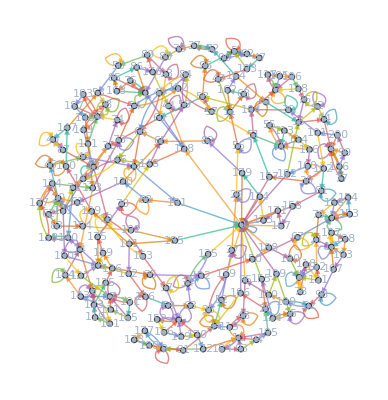

```mathematica
styles=ColorData[97]/@Range[Length[fn[[;;,3]]]];
g=multiGraph2[Flatten@Gather[(fn[[;;,1]]//Flatten)//DeleteDuplicates],fn[[;;,2]]//Flatten,fn[[;;,3]]//Flatten,styles,VertexSize->0.5,VertexLabels->Placed["Name",Center],ImageSize->Full, GraphLayout->"GravityEmbedding"]
```

```mathematica
Export["img.pdf",g]
```

img.pdf

```mathematica
SystemOpen["img.pdf"]
```

## Pre procesado para el decoding de las instrucciones de la TM

```mathematica
fn
```

{{{0},{0->0},{00R}},{{0},{0->128},{11L}},{{1},{1->1},{00R}},{{1},{1->75},{11R}},{{2},{2->2},{00R}},{{2},{2->152},{10R}},{{3},{3->3},{00R}},{{3},{3->78},{11R}},{{4},{4->4},{00R}},{{4},{4->77},{11R}},{{5},{5->5},{00L}},{{5},{5->90},{11L}},{{6},{6->6},{00L}},{{6},{6->117},{11L}},{{7},{7->7},{00R}},{{7},{7->153},{11R}},{{8},{8->8},{00R}},{{8},{8->161},{11R}},{{9},{9->9},{00L}},{{9},{9->177},{11L}},{{10},{10->10},{00L}},{{10},{10->184},{11L}},{{11},{11->11},{00R}},{{11},{11->68},{10L}},{{12},{12->12},{00L}},{{12},{12->197},{10L}},{{13},{13->19},{01R}},{{13},{13->13},{11R}},{{14},{14->8},{00R}},{{14},{14->14},{11R}},{{15},{15->42},{00R}},{{15},{15->64},{10R}},{{16},{16->16},{00L}},{{16},{16->55},{11L}},{{17},{17->17},{00L}},{{17},{17->191},{11L}},{{18},{18->35},{01L}},{{18},{18->140},{11L}},{{19},{19->19},{00R}},{{19},{19->163},{10R}},{{20},{20->45},{00R}},{{20},{20->20},{11R}},{{21},{21->12},{01L}},{{21},{21->21},{11L}},{{22},{22->22},{00L}},{{22},{22->109},{10L}},{{23},{23->60},{00R}},{{23},{23->23},{11L}},{{24},{24->52},{01R}},{{24},{24->24},{11R}},{{25},{25->25},{00R}},{{25},{25->124},{11R}},{{26},{26->186},{01R}},{{26},{26->26},{11L}},{{27},{27->29},{01L}},{{27},{27->27},{10R}},{{28},{28->28},{00L}},{{28},{28->149},{11L}},{{29},{29->29},{01L}},{{29},{29->56},{10L}},{{30},{30->104},{00R}},{{30},{30->30},{11L}},{{31},{31->13},{01R}},{{31},{31->74},{10L}},{{32},{32->32},{00L}},{{32},{32->183},{11L}},{{33},{33->181},{01L}},{{33},{33->33},{11L}},{{34},{34->34},{00L}},{{34},{34->135},{10L}},{{35},{35->35},{00L}},{{35},{35->132},{11L}},{{36},{36->36},{00L}},{{36},{36->139},{10L}},{{37},{37->72},{01R}},{{37},{37->38},{11L}},{{38},{38->38},{01R}},{{38},{38->80},{11R}},{{39},{39->157},{00R}},{{39},{39->39},{11L}},{{40},{40->40},{00L}},{{40},{40->87},{11L}},{{41},{41->15},{00R}},{{41},{41->41},{11R}},{{42},{42->42},{01R}},{{42},{42->64},{11R}},{{43},{43->66},{00R}},{{43},{43->66},{11R}},{{44},{44->128},{00R}},{{44},{44->44},{11L}},{{45},{45->46},{00R}},{{45},{45->45},{11R}},{{46},{46->33},{00L}},{{46},{46->46},{11R}},{{47},{47->5},{00L}},{{47},{47->193},{11L}},{{48},{48->48},{00R}},{{48},{48->115},{11R}},{{49},{49->11},{01R}},{{49},{49->49},{11L}},{{50},{50->53},{01L}},{{50},{50->50},{11R}},{{51},{51->104},{01L}},{{51},{51->16},{10L}},{{52},{52->52},{01R}},{{52},{52->27},{10R}},{{53},{53->28},{01L}},{{53},{53->54},{11L}},{{54},{54->112},{01L}},{{54},{54->112},{11L}},{{55},{55->16},{00L}},{{55},{55->113},{11L}},{{56},{56->11},{01R}},{{56},{56->56},{11L}},{{57},{57->51},{01L}},{{57},{57->58},{11L}},{{58},{58->60},{00L}},{{58},{58->96},{10L}},{{59},{59->84},{00R}},{{59},{59->84},{11R}},{{60},{60->31},{00L}},{{60},{60->128},{11R}},{{61},{61->20},{00R}},{{61},{61->62},{11L}},{{62},{62->20},{00R}},{{62},{62->83},{11L}},{{63},{63->34},{00L}},{{63},{63->36},{10L}},{{64},{64->4},{00R}},{{64},{64->64},{11R}},{{65},{65->66},{01L}},{{65},{65->59},{11R}},{{66},{66->146},{01L}},{{66},{66->33},{10L}},{{67},{67->7},{00R}},{{67},{67->67},{11R}},{{68},{68->68},{00L}},{{68},{68->162},{10L}},{{69},{69->63},{00L}},{{69},{69->69},{10L}},{{70},{70->148},{00L}},{{70},{70->70},{11R}},{{71},{71->140},{00L}},{{71},{71->31},{11L}},{{72},{72->37},{00R}},{{72},{72->37},{10R}},{{73},{73->54},{01L}},{{73},{73->73},{11L}},{{74},{74->32},{00L}},{{74},{74->74},{11L}},{{75},{75->1},{00R}},{{75},{75->168},{11R}},{{76},{76->15},{00R}},{{76},{76->76},{11L}},{{77},{77->4},{00R}},{{77},{77->196},{11R}},{{78},{78->3},{00R}},{{78},{78->118},{11R}},{{79},{79->7},{00R}},{{79},{79->21},{11L}},{{80},{80->1},{00R}},{{80},{80->80},{11R}},{{81},{81->158},{00L}},{{81},{81->81},{11R}},{{82},{82->65},{00R}},{{82},{82->82},{11L}},{{83},{83->20},{00R}},{{83},{83->194},{11L}},{{84},{84->43},{00R}},{{84},{84->43},{11R}},{{85},{85->1},{00R}},{{85},{85->86},{11R}},{{86},{86->1},{00R}},{{86},{86->176},{11R}},{{87},{87->40},{00L}},{{87},{87->13},{10R}},{{88},{88->120},{01L}},{{88},{88->88},{11L}},{{89},{89->23},{01L}},{{89},{89->50},{11R}},{{90},{90->5},{00L}},{{90},{90->92},{11L}},{{91},{91->9},{00L}},{{91},{91->24},{11R}},{{92},{92->5},{00L}},{{92},{92->47},{11L}},{{93},{93->10},{00L}},{{93},{93->94},{11L}},{{94},{94->10},{00L}},{{94},{94->195},{11L}},{{95},{95->0},{00R}},{{95},{95->48},{11R}},{{96},{96->5},{00L}},{{96},{96->96},{11L}},{{97},{97->2},{01R}},{{97},{97->97},{11R}},{{98},{98->22},{01L}},{{98},{98->98},{11L}},{{99},{99->4},{00R}},{{99},{99->200},{11R}},{{100},{100->3},{00R}},{{100},{100->100},{11R}},{{101},{101->30},{01L}},{{101},{101->102},{11R}},{{102},{102->39},{01L}},{{102},{102->81},{11R}},{{103},{103->12},{01L}},{{103},{103->107},{11L}},{{104},{104->58},{01L}},{{104},{104->6},{10L}},{{105},{105->6},{00L}},{{105},{105->106},{11L}},{{106},{106->6},{00L}},{{106},{106->108},{11L}},{{107},{107->12},{01L}},{{107},{107->98},{11L}},{{108},{108->6},{00L}},{{108},{108->76},{11L}},{{109},{109->22},{01L}},{{109},{109->110},{11L}},{{110},{110->95},{01R}},{{110},{110->199},{11R}},{{111},{111->17},{00L}},{{111},{111->143},{11L}},{{112},{112->57},{01L}},{{112},{112->57},{11L}},{{113},{113->16},{00L}},{{113},{113->114},{11L}},{{114},{114->16},{00L}},{{114},{114->116},{11L}},{{115},{115->48},{00R}},{{115},{115->24},{11R}},{{116},{116->16},{00L}},{{116},{116->160},{11L}},{{117},{117->6},{00L}},{{117},{117->105},{11L}},{{118},{118->3},{00R}},{{118},{118->121},{11R}},{{119},{119->8},{00R}},{{119},{119->123},{11R}},{{120},{120->65},{00R}},{{120},{120->61},{10L}},{{121},{121->3},{00R}},{{121},{121->122},{11R}},{{122},{122->3},{00R}},{{122},{122->21},{10L}},{{123},{123->8},{00R}},{{123},{123->125},{11R}},{{124},{124->25},{00R}},{{124},{124->155},{11L}},{{125},{125->8},{00R}},{{125},{125->126},{11R}},{{126},{126->18},{00L}},{{126},{126->159},{11R}},{{127},{127->18},{00L}},{{127},{127->17},{11L}},{{128},{128->148},{00L}},{{128},{128->1},{10R}},{{129},{129->129},{00L}},{{129},{129->130},{11L}},{{130},{130->147},{00L}},{{130},{130->130},{11L}},{{131},{131->190},{01R}},{{131},{131->71},{11L}},{{132},{132->150},{01L}},{{132},{132->132},{11L}},{{133},{133->14},{01R}},{{133},{133->73},{10L}},{{134},{134->133},{01L}},{{134},{134->131},{11R}},{{135},{135->34},{00L}},{{135},{135->0},{10H}},{{136},{136->136},{00L}},{{136},{136->69},{10L}},{{137},{137->134},{01L}},{{137},{137->134},{11R}},{{138},{138->137},{01L}},{{138},{138->137},{10R}},{{139},{139->36},{00L}},{{139},{139->0},{11H}},{{140},{140->138},{01L}},{{140},{140->138},{11L}},{{141},{141->129},{01L}},{{141},{141->142},{10R}},{{142},{142->18},{01L}},{{142},{142->136},{10L}},{{143},{143->17},{00L}},{{143},{143->144},{11L}},{{144},{144->14},{01R}},{{144},{144->144},{11L}},{{145},{145->71},{01L}},{{145},{145->131},{11L}},{{146},{146->145},{01L}},{{146},{146->145},{11L}},{{147},{147->40},{00L}},{{147},{147->53},{10R}},{{148},{148->65},{01L}},{{148},{148->146},{11L}},{{149},{149->28},{00L}},{{149},{149->13},{11R}},{{150},{150->188},{00R}},{{150},{150->67},{10R}},{{151},{151->32},{00L}},{{151},{151->133},{10L}},{{152},{152->2},{01R}},{{152},{152->166},{11R}},{{153},{153->7},{00R}},{{153},{153->154},{11R}},{{154},{154->7},{00R}},{{154},{154->156},{11R}},{{155},{155->0},{00R}},{{155},{155->26},{11L}},{{156},{156->7},{00R}},{{156},{156->79},{11R}},{{157},{157->0},{00R}},{{157},{157->51},{11R}},{{158},{158->0},{00R}},{{158},{158->167},{11L}},{{159},{159->18},{00L}},{{159},{159->175},{11R}},{{160},{160->182},{00R}},{{160},{160->160},{11L}},{{161},{161->8},{00R}},{{161},{161->119},{11R}},{{162},{162->11},{01R}},{{162},{162->164},{11L}},{{163},{163->19},{01R}},{{163},{163->97},{11R}},{{164},{164->72},{00R}},{{164},{164->41},{11R}},{{165},{165->17},{00L}},{{165},{165->111},{11L}},{{166},{166->2},{01R}},{{166},{166->169},{11R}},{{167},{167->0},{00R}},{{167},{167->171},{11L}},{{168},{168->1},{00R}},{{168},{168->85},{11R}},{{169},{169->2},{01R}},{{169},{169->170},{11R}},{{170},{170->2},{01R}},{{170},{170->172},{11R}},{{171},{171->0},{00R}},{{171},{171->173},{11L}},{{172},{172->9},{01L}},{{172},{172->10},{11L}},{{173},{173->0},{00R}},{{173},{173->174},{11L}},{{174},{174->0},{00R}},{{174},{174->179},{11L}},{{175},{175->18},{00L}},{{175},{175->70},{11R}},{{176},{176->44},{01L}},{{176},{176->89},{11R}},{{177},{177->9},{00L}},{{177},{177->178},{11L}},{{178},{178->9},{00L}},{{178},{178->180},{11L}},{{179},{179->0},{00R}},{{179},{179->82},{10L}},{{180},{180->9},{00L}},{{180},{180->91},{11L}},{{181},{181->0},{00R}},{{181},{181->88},{10L}},{{182},{182->0},{00R}},{{182},{182->15},{11R}},{{183},{183->32},{00L}},{{183},{183->187},{11L}},{{184},{184->10},{00L}},{{184},{184->93},{11L}},{{185},{185->0},{00R}},{{185},{185->141},{10R}},{{186},{186->0},{00R}},{{186},{186->24},{10R}},{{187},{187->32},{00L}},{{187},{187->189},{11L}},{{188},{188->0},{00R}},{{188},{188->100},{10R}},{{189},{189->32},{00L}},{{189},{189->151},{11L}},{{190},{190->18},{00L}},{{190},{190->127},{11R}},{{191},{191->17},{00L}},{{191},{191->165},{11L}},{{192},{192->185},{00R}},{{192},{192->192},{11R}},{{193},{193->5},{00L}},{{193},{193->49},{11L}},{{194},{194->20},{00R}},{{194},{194->192},{11R}},{{195},{195->10},{00L}},{{195},{195->26},{11L}},{{196},{196->4},{00R}},{{196},{196->99},{11R}},{{197},{197->12},{01L}},{{197},{197->198},{11L}},{{198},{198->12},{01L}},{{198},{198->103},{11L}},{{199},{199->0},{00R}},{{199},{199->25},{11R}},{{200},{200->4},{00R}},{{200},{200->101},{11R}}}

```mathematica
procesado=Table[{(*Estado inicial*)(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin //ToExpression,(*Estado siguiente*)(StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin//ToExpression,
(*Valor que leo*)(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last//ToExpression,
(*Valor que escribo*)(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]]//ToExpression,
(*Movimiento*)(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last//ToExpression},
{i,1,Length[MT]}];
Export["procesado.csv", procesado]
```

procesado.csv

```mathematica
procesado[[2]]
```

{0,10000000,1,1,L}

```mathematica
(StringSplit[MT[[2]],"->"][[2]]//Characters)[[;;-3]]//StringJoin
```

10000000

```mathematica
(StringSplit[MT[[2]],"->"][[2]]//Characters)
```

{1,0,0,0,0,0,0,0,1,L}